```mathematica
SetDirectory[NotebookDirectory[]];
data = SetPrecision[Import["write.dat"],16];

(*Reads the diameter value from the 4th row*)
d= data[[4]][[1]];
r=d/2;

(*Centre positions are stored from the 7th row onwards*)
(*Create a table with the "Circle" graphics objects*)
graphicsset =Table[
Circle[data[[i]],r],
{i,7,Length[data]}
];

(*Find the dimensions of the enclosing box*)
{xmin,ymin}=Min/@Transpose[data[[7;;]]];
{xmax,ymax}=Max/@Transpose[data[[7;;]]];
volume = (xmax-xmin) * (ymax-ymin) ;
occupied = (Length[data]-6) * π*r^2;

packfraction = occupied/volume;
```

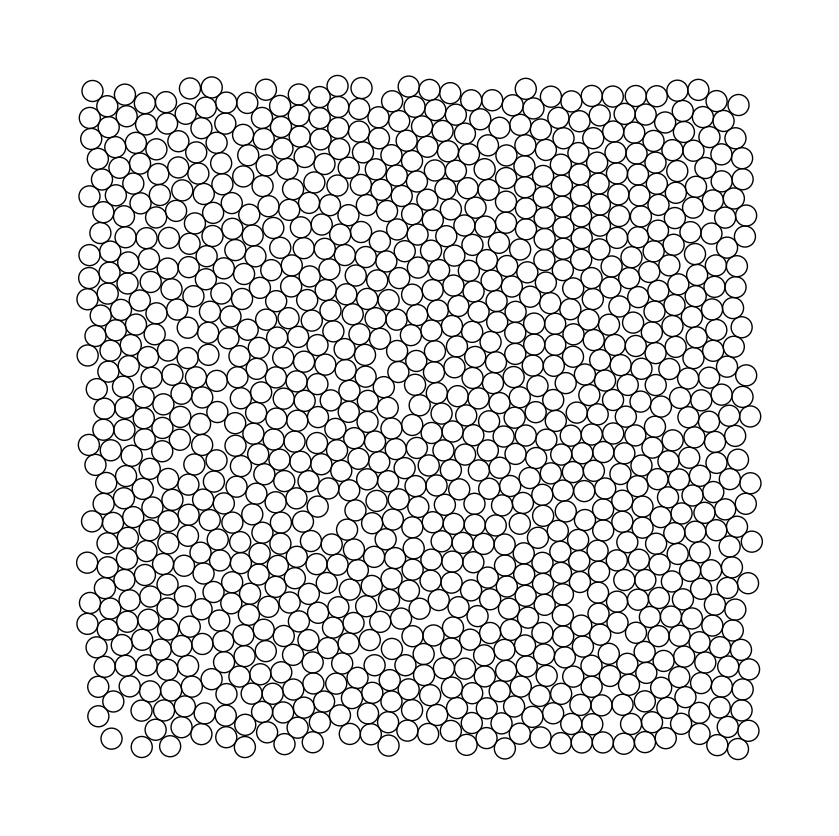

0.787829541459411

```mathematica
(* For 2D packing! *)
Graphics[graphicsset]
packfraction
```

```mathematica
DistTable = ParallelTable[
{data[[i]],Norm[data[[i]]-data[[j]]]},
{i,7,Length[data]},
{j,7,Length[data]}
];
```

```mathematica
FilteredDistTable=Select[DistTable,#[[1]][[1]]-xmin>2d && xmax-#[[1]][[1]]>2d && #[[1]][[2]]-ymin>2d && ymax-#[[1]][[2]]>2d &];
```

```mathematica
TouchingCircles=(Count[DistanceBtwCentres_/;DistanceBtwCentres<1.001*d]/@OldDistTable)-1;
N[Mean[TouchingCircles]]
Tally[TouchingCircles]
```

2.754

{{3,401},{4,213},{5,46},{0,64},{2,193},{1,83}}

```mathematica
FilteredData = Select[data[[7;;]],#[[1]]-xmin>2d && xmax-#[[1]]>2d && #[[2]]-ymin>2d && ymax-#[[2]]>2d &];
Length[FilteredData]
```